# Spiral Repellor

## Non-Compact Phase Spaces

### Non - Compact x - z Phase Space

```mathematica
(*Define the parameters for this case*)
wx=-0.5;
q=1;
ϵ=-0.25;
```

```mathematica
(*Define the dynamical system for coupled dark matter (z) and dark energy (x)*)
dex:=x'=-3*x*(1+wx+ϵ*x)-q*x*z
dez:=z'=-3*z + q*x*z
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{dex==0,dez==0},{x,z}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→2.,z→0.},{x→3.,z→0.75},{x→0.,z→0.}}

```mathematica
FP[1]={x/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],z/.FPs[[2,2]]};
FP[3]={x/.FPs[[3,1]],z/.FPs[[3,2]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,3}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[dex,x],D[dex,z]}, {D[dez,x],D[dez,z]}}];
J//MatrixForm
```

(-1.5+1.5 x-1. z | -x
z | -3+x)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(2.
0.) | (1.5 | -2.
0. | -1.) | (1.5
-1.) | (1. | 0.
0.624695 | 0.780869)
(3.
0.75) | (2.25 | -3.
0.75 | 0.) | (1.125+0.992157 ⅈ
1.125-0.992157 ⅈ) | (0.894427+0. ⅈ | 0.33541-0.295804 ⅈ
0.894427+0. ⅈ | 0.33541+0.295804 ⅈ)
(0.
0.) | (-1.5 | 0.
0. | -3.) | (-3.
-1.5) | (0. | 1.
-1. | 0.)

```mathematica
(*Find condition for first fixed point to be complex*)
wxCond=Solve[4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2==0,{q,ϵ,wx}]
```

Solve::ivar: 1 is not a valid variable.

Solve[False,{1,-0.25,-0.5}]

```mathematica
wxCondition=wx/.wxCond[[1]]
```

ReplaceAll::reps: {False} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-0.5/.False

```mathematica
(*Maximum value wx can be for the first fixed point to be complex for positive q and negative ϵ -> Fig. 9b*)
(*For this wx the two eigenvalues are the same*)
wxMax=wxCondition/.{ϵ->-0.25,q->1}
```

-0.5/.False

```mathematica
(*Define the differential equations in terms of their variables*)
DE[wx_,q_,ϵ_]=dex;
DM[q_]=dez;
```

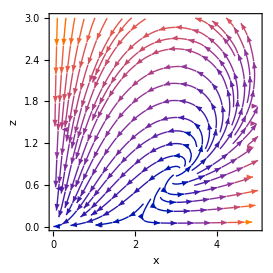

```mathematica
StreamPlot[{DE[wx,q,ϵ],DM[q]},{x,0,5},{z,0,3},FrameLabel->{"x","z"}]
```

### Non-Compact x - y - z Phase Space

```mathematica
(*Define the dynamical system for coupled dark matter (z) and dark energy (x)*)
de1:=x'=-3*y*x*(1+wx+ϵ*x)-q*x*y*z
de2:=y'=-y^2-(1/6)*(x+z+3*wx*x+3*ϵ*x^2)
de3:=z'=-3*y*z + q*x*y*z
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{de1==0,de2==0,de3==0},{x,y,z}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→0.,z→0.25 x (2.+3. x)},{x→0.,y→0.,z→0.},{x→2.,y→-0.816497,z→0.},{x→2.,y→0.816497,z→0.},{x→3.,y→-1.11803,z→0.75},{x→3.,y→1.11803,z→0.75}}

```mathematica
(*Remove arrows from fixed points and put them into a common variable name*)
FP[1]={x,y/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],y/.FPs[[2,2]],z/.FPs[[2,3]]};
FP[3]={x/.FPs[[3,1]],y/.FPs[[3,2]],z/.FPs[[3,3]]};
FP[4]={x/.FPs[[4,1]],y/.FPs[[4,2]],z/.FPs[[4,3]]};
FP[5]={x/.FPs[[5,1]],y/.FPs[[5,2]],z/.FPs[[5,3]]};
FP[6]={x/.FPs[[6,1]],y/.FPs[[6,2]],z/.FPs[[6,3]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,6}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[de1,x],D[de1,y],D[de1,z]}, {D[de2,x],D[de2,y],D[de2,z]},{D[de3,x],D[de3,y],D[de3,z]}}];
J//MatrixForm
```

(y (-1.5+1.5 x-1. z) | x (-1.5+0.75 x-z) | -x y
0.0833333+0.25 x | -2 y | -1/6
y z | (-3+x) z | (-3+x) y)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm},{i,1,6}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(x
0.
0.25 x (2.+3. x)) | (0. | -0.75 x (2.-0.333333 x+1. x^2) | 0.
0.0833333+0.25 x | 0. | -1/6
0. | 0.75 (-3.+x) x (0.666667+1. x) | 0.) | (0
(0.-0.433013 ⅈ) √x √(-0.604794+1. x) √(1.1023+1.27146 x+1. x^2)
(0.+0.433013 ⅈ) √x √(-0.604794+1. x) √(1.1023+1.27146 x+1. x^2)) | (0.666667/(0.333333+1. x) | 0 | 1.
-(1. (0.666667+1.88889 x+1. x^3))/((-3.+x) (0.333333+1. x) (0.666667+1. x)) | -((0.+0.57735 ⅈ) √(-0.604794+1. x) √(1.1023+1.27146 x+1. x^2))/((-3.+x) √x (0.666667+1. x)) | 1.
-(1. (0.666667+1.88889 x+1. x^3))/((-3.+x) (0.333333+1. x) (0.666667+1. x)) | ((0.+0.57735 ⅈ) √(-0.604794+1. x) √(1.1023+1.27146 x+1. x^2))/((-3.+x) √x (0.666667+1. x)) | 1.)
(0.
0.
0.) | (0. | 0. | 0.
0.0833333 | 0. | -1/6
0. | 0. | 0.) | (0.
0.
0.) | (0. | 1. | 0.
0. | 0. | 0.
0. | 0. | 0.)
(2.
-0.816497
0.) | (-1.22474 | 0. | 1.63299
0.583333 | 1.63299 | -1/6
0. | 0. | 0.816497) | (1.63299
-1.22474
0.816497) | (0. | 1. | 0.
0.979796 | -0.2 | 0.
0.600469 | -0.275783 | 0.750587)
(2.
0.816497
0.) | (1.22474 | 0. | -1.63299
0.583333 | -1.63299 | -1/6
0. | 0. | -0.816497) | (-1.63299
1.22474
-0.816497) | (0. | 1. | 0.
0.979796 | 0.2 | 0.
0.600469 | 0.275783 | 0.750587)
(3.
-1.11803
0.75) | (-2.51558 | 0. | 3.3541
0.833333 | 2.23607 | -1/6
-0.838525 | 0. | 0.) | (2.23607+0. ⅈ
-1.25779+1.10926 ⅈ
-1.25779-1.10926 ⅈ) | (0.+0. ⅈ | 1.+0. ⅈ | 0.+0. ⅈ
0.878938+0. ⅈ | -0.180158-0.0433322 ⅈ | 0.329602+0.290681 ⅈ
0.878938+0. ⅈ | -0.180158+0.0433322 ⅈ | 0.329602-0.290681 ⅈ)
(3.
1.11803
0.75) | (2.51558 | 0. | -3.3541
0.833333 | -2.23607 | -1/6
0.838525 | 0. | 0.) | (-2.23607+0. ⅈ
1.25779+1.10926 ⅈ
1.25779-1.10926 ⅈ) | (0.+0. ⅈ | 1.+0. ⅈ | 0.+0. ⅈ
0.878938+0. ⅈ | 0.180158-0.0433322 ⅈ | 0.329602-0.290681 ⅈ
0.878938+0. ⅈ | 0.180158+0.0433322 ⅈ | 0.329602+0.290681 ⅈ)

```mathematica
Eq1[q_,wx_,ϵ_]=de1;
Eq2[wx_,ϵ_]=de2;
Eq3[q_]=de3;
```

```mathematica
StreamPlot3D[{Eq1[q,wx,ϵ],Eq2[wx,ϵ],Eq3[q]},{x,0,15},{y,-5,5},{z,0,10},AxesLabel->{"x","y","z"}]
```

-Graphics3D-

## Non-Compact Numeric Phase Spaces

### x - y - z

```mathematica
(*Clear all variables*)
ClearAll["Global`*"];
```

```mathematica
(*Define the dynamical system for coupled dark matter (z) and dark energy (x)*)
de1:=x'=-3*y*x*(1+wx+ϵ*x)-q*x*y*z
de2:=y'=-y^2-(1/6)*(x+z+3*wx*x+3*ϵ*x^2)
de3:=z'=-3*y*z + q*x*y*z
```

```mathematica
q=1;
wx=-0.5;
ϵ=-0.25;
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{de1==0,de2==0,de3==0},{x,y,z}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→0.,z→0.25 x (2.+3. x)},{x→0.,y→0.,z→0.},{x→2.,y→-0.816497,z→0.},{x→2.,y→0.816497,z→0.},{x→3.,y→-1.11803,z→0.75},{x→3.,y→1.11803,z→0.75}}

```mathematica
(*Remove arrows from fixed points and put them into a common variable name*)
FP[1]={x,y/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],y/.FPs[[2,2]],z/.FPs[[2,3]]};
FP[3]={x/.FPs[[3,1]],y/.FPs[[3,2]],z/.FPs[[3,3]]};
FP[4]={x/.FPs[[4,1]],y/.FPs[[4,2]],z/.FPs[[4,3]]};
FP[5]={x/.FPs[[5,1]],y/.FPs[[5,2]],z/.FPs[[5,3]]};
FP[6]={x/.FPs[[6,1]],y/.FPs[[6,2]],z/.FPs[[6,3]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,6}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[de1,x],D[de1,y],D[de1,z]}, {D[de2,x],D[de2,y],D[de2,z]},{D[de3,x],D[de3,y],D[de3,z]}}];
J//MatrixForm
```

(y (-1.5+1.5 x-1. z) | x (-1.5+0.75 x-z) | -x y
0.0833333+0.25 x | -2 y | -1/6
y z | (-3+x) z | (-3+x) y)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm},{i,1,6}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(x
0.
0.25 x (2.+3. x)) | (0. | -0.75 x (2.-0.333333 x+1. x^2) | 0.
0.0833333+0.25 x | 0. | -1/6
0. | 0.75 (-3.+x) x (0.666667+1. x) | 0.) | (0
(0.-0.433013 ⅈ) √x √(-0.604794+1. x) √(1.1023+1.27146 x+1. x^2)
(0.+0.433013 ⅈ) √x √(-0.604794+1. x) √(1.1023+1.27146 x+1. x^2)) | (0.666667/(0.333333+1. x) | 0 | 1.
-(1. (0.666667+1.88889 x+1. x^3))/((-3.+x) (0.333333+1. x) (0.666667+1. x)) | -((0.+0.57735 ⅈ) √(-0.604794+1. x) √(1.1023+1.27146 x+1. x^2))/((-3.+x) √x (0.666667+1. x)) | 1.
-(1. (0.666667+1.88889 x+1. x^3))/((-3.+x) (0.333333+1. x) (0.666667+1. x)) | ((0.+0.57735 ⅈ) √(-0.604794+1. x) √(1.1023+1.27146 x+1. x^2))/((-3.+x) √x (0.666667+1. x)) | 1.)
(0.
0.
0.) | (0. | 0. | 0.
0.0833333 | 0. | -1/6
0. | 0. | 0.) | (0.
0.
0.) | (0. | 1. | 0.
0. | 0. | 0.
0. | 0. | 0.)
(2.
-0.816497
0.) | (-1.22474 | 0. | 1.63299
0.583333 | 1.63299 | -1/6
0. | 0. | 0.816497) | (1.63299
-1.22474
0.816497) | (0. | 1. | 0.
0.979796 | -0.2 | 0.
0.600469 | -0.275783 | 0.750587)
(2.
0.816497
0.) | (1.22474 | 0. | -1.63299
0.583333 | -1.63299 | -1/6
0. | 0. | -0.816497) | (-1.63299
1.22474
-0.816497) | (0. | 1. | 0.
0.979796 | 0.2 | 0.
0.600469 | 0.275783 | 0.750587)
(3.
-1.11803
0.75) | (-2.51558 | 0. | 3.3541
0.833333 | 2.23607 | -1/6
-0.838525 | 0. | 0.) | (2.23607+0. ⅈ
-1.25779+1.10926 ⅈ
-1.25779-1.10926 ⅈ) | (0.+0. ⅈ | 1.+0. ⅈ | 0.+0. ⅈ
0.878938+0. ⅈ | -0.180158-0.0433322 ⅈ | 0.329602+0.290681 ⅈ
0.878938+0. ⅈ | -0.180158+0.0433322 ⅈ | 0.329602-0.290681 ⅈ)
(3.
1.11803
0.75) | (2.51558 | 0. | -3.3541
0.833333 | -2.23607 | -1/6
0.838525 | 0. | 0.) | (-2.23607+0. ⅈ
1.25779+1.10926 ⅈ
1.25779-1.10926 ⅈ) | (0.+0. ⅈ | 1.+0. ⅈ | 0.+0. ⅈ
0.878938+0. ⅈ | 0.180158-0.0433322 ⅈ | 0.329602-0.290681 ⅈ
0.878938+0. ⅈ | 0.180158+0.0433322 ⅈ | 0.329602+0.290681 ⅈ)

```mathematica
(*Define the dynamical system for coupled dark matter (z) and dark energy (x)*)
de1t:=x1'[t]==-3*y1[t]*x1[t]*(1+wx+ϵ*x1[t])-q*x1[t]*y1[t]*z1[t]
de2t:=y1'[t]==-y1[t]^2-(1/6)*(x1[t]+z1[t]+3*wx*x1[t]+3*ϵ*x1[t]^2)
de3t:=z1'[t]==-3*y1[t]*z1[t]+ q*x1[t]*y1[t]*z1[t]
de4t=a1'[t]==a1[t]*y1[t];
```

```mathematica
q=1;
wx=-0.5;
ϵ=-0.25;
```

```mathematica
(*Analyse the unstable spiral fixed point*)
(*z and y values at the spiral point for this case*)
zSpiral=-(3 (q+q wx+3 ϵ))/q^2
ySpiralPlus=(√(-q wx-3 ϵ))/q
ySpiralMinus=-(√(-q wx-3 ϵ))/q
```

0.75

1.11803

-1.11803

```mathematica
(*Find the eigenvalues when taking the negative root for y value at spiral fixed point*)
Eig1=(2 √(-q wx-3 ϵ))/q
```

2.23607

```mathematica
Eig2=1/(2 q^2)3 (3 √(-q wx-3 ϵ) ϵ-√(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3))
```

-1.25779-1.10926 ⅈ

```mathematica
1/(2 q^2)(Eig3=3 (3 √(-q wx-3 ϵ) ϵ+√(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3)))
```

-1.25779+1.10926 ⅈ

```mathematica
(*Find the eigenvalues when taking the positive root for y value at spiral fixed point*)
Eig4=-(2 √(-q wx-3 ϵ))/q
```

-2.23607

```mathematica
Eig5=1/(2 q^2)3 (-3 √(-q wx-3 ϵ) ϵ-√(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3))
```

1.25779-1.10926 ⅈ

```mathematica
Eig6=1/(2 q^2)3 (-3 √(-q wx-3 ϵ) ϵ+√(-4 q^3 wx-4 q^3 wx^2-12 q^2 ϵ-24 q^2 wx ϵ-36 q ϵ^2-9 q wx ϵ^2-27 ϵ^3))
```

1.25779+1.10926 ⅈ

```mathematica
traj[x0_,y0_,z0_,a0_]=NDSolve[{de1t,de2t,de3t,de4t, x1[0]==x0,y1[0]==y0,z1[0]==z0,a1[0]==a0}, {x1,y1,z1,a1},{t,-50,50}];
```

NDSolve::ndinnt: Initial condition a0 is not a number or a rectangular array of numbers.

```mathematica
sol[1]=traj[2,0.1,0.009,1];
sol[2]=traj[0.5,0.1,0.009,0.5];
sol[3]=traj[5,0.1,0.009,0.3];
sol[4]=traj[4,0.1,0.009,0.1];
sol[5]=traj[1,0.1,0.009,0.7];
sol[6]=traj[3,2,0.009,0.9];
sol[7]=traj[4,3,0.009,0.05];
sol[8]=traj[1,2.5,0.009,0.6];
```

NDSolve::ndsz: At t == -0.553018, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == -0.353627, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == -0.406503, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-49.998} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dprec: The precision of input value {-49.998} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dprec: The precision of input value {-47.9571} and/or the interpolation grid is insufficient to compute the value.

General::stop: Further output of InterpolatingFunction::dprec will be suppressed during this calculation.

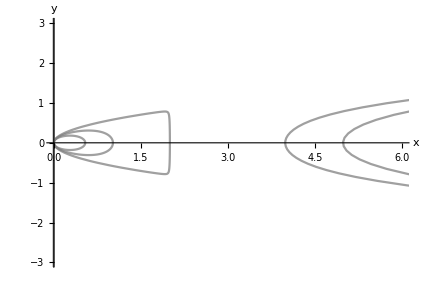

```mathematica
ParametricPlot[Evaluate[Table[{x1[t],y1[t]}/.sol[i],{i,1,8}], {t,-50,50},PlotStyle -> {{Gray, Opacity[0.75]}},PlotRange->{{0,6},{-3,3}}],AxesLabel->{"x","y"}]
```

InterpolatingFunction::dmval: Input value {-49.998} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dprec: The precision of input value {-49.998} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dprec: The precision of input value {-47.9571} and/or the interpolation grid is insufficient to compute the value.

General::stop: Further output of InterpolatingFunction::dprec will be suppressed during this calculation.

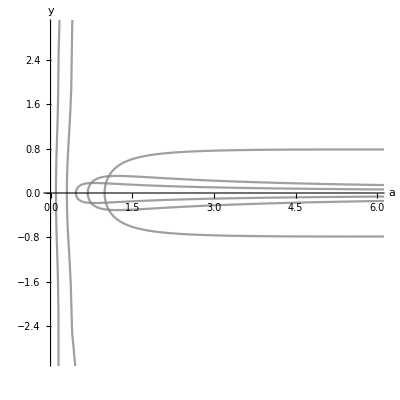

```mathematica
ParametricPlot[Evaluate[Table[{a1[t],y1[t]}/.sol[i],{i,1,8}], {t,-50,50},PlotStyle -> {{Gray, Opacity[0.75]}},PlotRange->{{0,6},{-3,3}}],AxesLabel->{"a","y"}]
```

### Non-Compact Ωx-Ωm Density Parameter Phase Space

#### Flat Case

```mathematica
deΩx:=Ωx'=Ωx*(-(1+3*wx)+Ωx*(-3*(ϵ/Ωs)+1+3*wx+3*ϵ*(Ωx/Ωs))+(1-Ωx)*(1-q/Ωs))
deΩs:=Ωs'=Ωs*(2+Ωx*(1+3*wx+3*ϵ*Ωx/Ωs)+(1-Ωx))
```

```mathematica
q=1;
wx=-0.5;
ϵ=-0.25;
```

```mathematica
(*Define the differential equations in terms of their variables*)
DE[wx_,q_,ϵ_]=deΩx;
DS[wx_,q_,ϵ_]=deΩs;
```

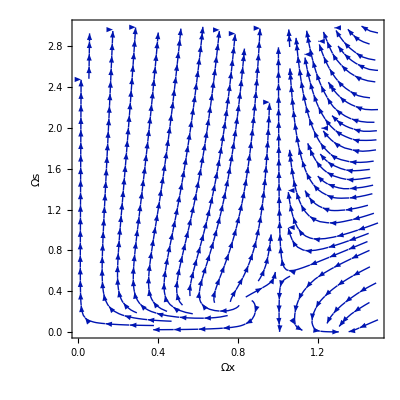

```mathematica
PhaseSpaceFlatΩ=StreamPlot[{DE[wx,q,ϵ],DS[wx,q,ϵ]},{Ωx,0,1.5},{Ωs,0,3},FrameLabel->{"Ωx","Ωs"}]
```

#### Full Case

```mathematica
(*Define the dynamical system for coupled dark matter (z) and dark energy (x)*)
deΩx:=Ωx'=Ωx*(-(1+3*wx)+Ωx*(-3*(ϵ/Ωs)+1+3*wx+3*ϵ*(Ωx/Ωs))+Ωm*(1-q/Ωs))
deΩm:=Ωm'=Ωm*(-1+Ωm+Ωx*((q/Ωs)+1+3*wx+3*ϵ*Ωx/Ωs))
deΩs:=Ωs'=Ωs*(2+Ωx*(1+3*wx+3*ϵ*Ωx/Ωs)+Ωm)
```

```mathematica
q=1;
wx=-0.5;
ϵ=-0.25;
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{deΩx==0,deΩm==0,deΩs==0},{Ωx,Ωm,Ωs}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Ωx→-2.,Ωm→0.,Ωs→1.},{Ωx→0.5,Ωm→-0.625,Ωs→0.166667}}

```mathematica
(*Define the differential equations in terms of their variables*)
DE[wx_,q_,ϵ_]=deΩx;
DM[wx_,q_,ϵ_]=deΩm;
DS[wx_,q_,ϵ_]=deΩs;
```

```mathematica
PhaseSpaceΩ=StreamPlot3D[{DE[wx,q,ϵ],DM[wx,q,ϵ],DS[wx,q,ϵ]},{Ωx,0,1.5},{Ωm,0,1.5},{Ωs,0,3},AxesLabel->{"Ωx","Ωm","Ωs"},StreamMarkers->"Arrow"]
```

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$185580'[System`VectorPlotsDump`t$185580]=={System`VectorPlotsDump`w$185580 (0.5+Plus[«2»] Plus[«2»]+Indexed[«2»] Plus[«3»]),DM[-0.5,1,-0.25],(3-Indexed[«2»]+Indexed[«2»] Plus[«2»]) System`VectorPlotsDump`w$185580,√(DM[«3»]^2+Power[«2»] Power[«2»]+Power[«2»] Power[«2»])},System`VectorPlotsDump`w$185580[0]=={0.15,0.15,0.3,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$185580,{System`VectorPlotsDump`t$185580,-∞,0.},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$185580'[System`VectorPlotsDump`t$185580]=={System`VectorPlotsDump`w$185580 (0.5+Plus[«2»] Plus[«2»]+Indexed[«2»] Plus[«3»]),DM[-0.5,1,-0.25],(3-Indexed[«2»]+Indexed[«2»] Plus[«2»]) System`VectorPlotsDump`w$185580,√(DM[«3»]^2+Power[«2»] Power[«2»]+Power[«2»] Power[«2»])},System`VectorPlotsDump`w$185580[0]=={0.15,0.15,0.3,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$185580,{System`VectorPlotsDump`t$185580,0.,∞},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$185580,System`VectorPlotsDump`linesxmax$185580},{System`VectorPlotsDump`linesymin$185580,System`VectorPlotsDump`linesymax$185580},{System`VectorPlotsDump`lineszmin$185580,System`VectorPlotsDump`lineszmax$185580},{System`VectorPlotsDump`linesfieldmin$185580,System`VectorPlotsDump`linesfieldmax$185580}} and System`VectorPlotsDump`extremes$185687 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$185580'[System`VectorPlotsDump`t$185580]=={System`VectorPlotsDump`w$185580 (0.5+Plus[«2»] Plus[«2»]+Indexed[«2»] Plus[«3»]),DM[-0.5,1,-0.25],(3-Indexed[«2»]+Indexed[«2»] Plus[«2»]) System`VectorPlotsDump`w$185580,√(DM[«3»]^2+Power[«2»] Power[«2»]+Power[«2»] Power[«2»])},System`VectorPlotsDump`w$185580[0]=={0.15,0.15,1.1,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$185580,{System`VectorPlotsDump`t$185580,-∞,0.},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$185580'[System`VectorPlotsDump`t$185580]=={System`VectorPlotsDump`w$185580 (0.5+Plus[«2»] Plus[«2»]+Indexed[«2»] Plus[«3»]),DM[-0.5,1,-0.25],(3-Indexed[«2»]+Indexed[«2»] Plus[«2»]) System`VectorPlotsDump`w$185580,√(DM[«3»]^2+Power[«2»] Power[«2»]+Power[«2»] Power[«2»])},System`VectorPlotsDump`w$185580[0]=={0.15,0.15,1.1,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$185580,{System`VectorPlotsDump`t$185580,0.,∞},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$185580,System`VectorPlotsDump`linesxmax$185580},{System`VectorPlotsDump`linesymin$185580,System`VectorPlotsDump`linesymax$185580},{System`VectorPlotsDump`lineszmin$185580,System`VectorPlotsDump`lineszmax$185580},{System`VectorPlotsDump`linesfieldmin$185580,System`VectorPlotsDump`linesfieldmax$185580}} and System`VectorPlotsDump`extremes$185789 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$185580'[System`VectorPlotsDump`t$185580]=={System`VectorPlotsDump`w$185580 (0.5+Plus[«2»] Plus[«2»]+Indexed[«2»] Plus[«3»]),DM[-0.5,1,-0.25],(3-Indexed[«2»]+Indexed[«2»] Plus[«2»]) System`VectorPlotsDump`w$185580,√(DM[«3»]^2+Power[«2»] Power[«2»]+Power[«2»] Power[«2»])},System`VectorPlotsDump`w$185580[0]=={0.15,0.15,1.9,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$185580,{System`VectorPlotsDump`t$185580,-∞,0.},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$185580'[System`VectorPlotsDump`t$185580]=={System`VectorPlotsDump`w$185580 (0.5+Plus[«2»] Plus[«2»]+Indexed[«2»] Plus[«3»]),DM[-0.5,1,-0.25],(3-Indexed[«2»]+Indexed[«2»] Plus[«2»]) System`VectorPlotsDump`w$185580,√(DM[«3»]^2+Power[«2»] Power[«2»]+Power[«2»] Power[«2»])},System`VectorPlotsDump`w$185580[0]=={0.15,0.15,1.9,0.},WhenEvent[«1»,StopIntegration]},System`VectorPlotsDump`w$185580,{System`VectorPlotsDump`t$185580,0.,∞},ExtrapolationHandler→{Indeterminate&,WarningMessage→True},Method→Automatic] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$185580,System`VectorPlotsDump`linesxmax$185580},{System`VectorPlotsDump`linesymin$185580,System`VectorPlotsDump`linesymax$185580},{System`VectorPlotsDump`lineszmin$185580,System`VectorPlotsDump`lineszmax$185580},{System`VectorPlotsDump`linesfieldmin$185580,System`VectorPlotsDump`linesfieldmax$185580}} and System`VectorPlotsDump`extremes$185885 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Part::pkspec1: The expression System`VectorPlotsDump`i cannot be used as a part specification.

Part::pkspec1: The expression 1+System`VectorPlotsDump`i cannot be used as a part specification.

Function::fpct: Too many parameters in {System`VectorPlotsDump`x$,System`VectorPlotsDump`y$,System`VectorPlotsDump`z$} to be filled from Function[{System`VectorPlotsDump`x$,System`VectorPlotsDump`y$,System`VectorPlotsDump`z$},(True&)[System`VectorPlotsDump`x$,System`VectorPlotsDump`y$,System`VectorPlotsDump`z$]&&0≤System`VectorPlotsDump`x$≤1.5&&0≤System`VectorPlotsDump`y$≤1.5&&0≤System`VectorPlotsDump`z$≤3][1/2,System`VectorPlotsDump`i+If[If[PropertyValue[Interpolation[«1»],ValuesOnGrid]⟦All,4⟧>PropertyValue[Interpolation[«1»],ValuesOnGrid]⟦All,4⟧],If[Table[Take[Interpolation[Part[«3»]][System`VectorPlotsDump`tofs$185687[«1»]],3],{Charting`s,PropertyValue[«2»]⟦All,4⟧,PropertyValue[«2»]⟦All,4⟧,System`VectorPlotsDump`delta$185687}]],If[{}]]].

General::stop: Further output of Function::fpct will be suppressed during this calculation.

Part::pkspec1: The expression System`VectorPlotsDump`i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

```mathematica
deΩxt:=Ωx1'[t]==Ωx1[t]*(-(1+3*wx)+Ωx1[t]*(-3*(ϵ/Ωs1[t])+1+3*wx+3*ϵ*(Ωx1[t]/Ωs1[t]))+Ωm1[t]*(1-q/Ωs1[t]))
deΩmt:=Ωm1'[t]==Ωm1[t]*(-1+Ωm1[t]+Ωx1[t]*((q/Ωs1[t])+1+3*wx+3*ϵ*Ωx1[t]/Ωs1[t]))
deΩst:=Ωs1'[t]==Ωs1[t]*(2+Ωx1[t]*(1+3*wx+3*ϵ*Ωx1[t]/Ωs1[t])+Ωm1[t])
```

```mathematica
traj[x0_,z0_,s0_]=NDSolve[{deΩxt,deΩmt,deΩst,Ωx1[0]==x0,Ωm1[0]==z0,Ωs1[0]==s0}, {Ωx1,Ωm1,Ωs1},{t,-100,100}];
```

NDSolve::ndinnt: Initial condition z0 is not a number or a rectangular array of numbers.

```mathematica
sol[1]=traj[0.6889,0.3111,1];
```

NDSolve::ndsz: At t == -0.582981, step size is effectively zero; singularity or stiff system suspected.

```mathematica
sol[2]=traj[0.5,0.5,1];
```

NDSolve::ndsz: At t == -0.674911, step size is effectively zero; singularity or stiff system suspected.

```mathematica
PhaseSpaceΩ2=ParametricPlot3D[Evaluate[Table[{Ωx1[t],Ωm1[t],Ωs1[t]}/.sol[i],{i,1,2}], {t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],AxesLabel->{"Ωx","Ωm","Ωs"}];
```

InterpolatingFunction::dmval: Input value {-99.9959} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Show[PhaseSpaceΩ,PhaseSpaceΩ2]
```

-Graphics3D-

### Non-Compact Ωx-H-Ωm Density Parameter Phase Space

#### Flat Case

```mathematica
deΩx:=Ωx'=Ωx*H*(-(1+3*wx)+Ωx*(-3*(ϵ/Ωs)+1+3*wx+3*ϵ*(Ωx/Ωs))+(1-Ωx)*(1-q/Ωs))
deH:=H'=-H^2-(H^2/2)*(Ωx*(1+3*wx)+(1-Ωx)+3*ϵ*Ωx^2/Ωs)
deΩs:=Ωs'=Ωs*H*(2+Ωx*(1+3*wx+3*ϵ*Ωx/Ωs)+(1-Ωx))
```

```mathematica
q=1;
wx=-0.5;
ϵ=-0.25;
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{deΩx==0,deH==0,deΩs==0},{Ωx,H,Ωs}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{H→0.},{Ωx→0.8,Ωs→0.266667},{Ωx→1.,Ωs→0.5}}

```mathematica
(*Define the differential equations in terms of their variables*)
DE[wx_,q_,ϵ_]=deΩx;
HEqn[wx_,q_,ϵ_]=deH;
DS[wx_,q_,ϵ_]=deΩs;
```

```mathematica
PhaseSpaceΩ3D=StreamPlot3D[{DE[wx,q,ϵ],HEqn[wx,q,ϵ],DS[wx,q,ϵ]},{Ωx,0,1.5},{H,-1.5,1.5},{Ωs,0,1.5},AxesLabel->{"Ωx","H","Ωs"},StreamMarkers->"Arrow"]
```

-Graphics3D-

#### Full Case

```mathematica
deΩxt:=Ωx1'[t]==Ωx1[t]*H1[t]*(-(1+3*wx)+Ωx1[t]*(-3*(ϵ/Ωs1[t])+1+3*wx+3*ϵ*(Ωx1[t]/Ωs1[t]))+Ωm1[t]*(1-q/Ωs1[t]))
deHt:=H1'[t]==-H1[t]^2-(H1[t]^2/2)*(Ωx1[t]*(1+3*wx)+Ωm1[t]+3*ϵ*Ωx1[t]^2/Ωs1[t])
deΩmt:=Ωm1'[t]==Ωm1[t]*H1[t]*(-1+Ωm1[t]+Ωx1[t]*((q/Ωs1[t])+1+3*wx+3*ϵ*Ωx1[t]/Ωs1[t]))
deΩst:=Ωs1'[t]==Ωs1[t]*H1[t]*(2+Ωx1[t]*(1+3*wx+3*ϵ*Ωx1[t]/Ωs1[t])+Ωm1[t])
```

```mathematica
traj[x0_,H0_,z0_,s0_]=NDSolve[{deΩxt,deHt,deΩmt,deΩst, Ωx1[0]==x0,H1[0]==H0,Ωm1[0]==z0,Ωs1[0]==s0}, {Ωx1,H1,Ωm1,Ωs1},{t,-100,100}];
```

NDSolve::ndinnt: Initial condition H0 is not a number or a rectangular array of numbers.

```mathematica
sol[1]=traj[0.6889,0.5,0.3111,1];
sol[2]=traj[0.6889,0.7,0.3111,1];
sol[3]=traj[0.6889,1,0.3111,1];
sol[4]=traj[0.6889,-0.5,0.3111,1];
sol[5]=traj[0.6889,-0.7,0.3111,1];
sol[6]=traj[0.6889,-1,0.3111,1];
sol[7]=traj[0.6889,0.3,0.3111,1];
sol[8]=traj[0.6889,0.1,0.3111,1];
sol[9]=traj[0.6889,-0.3,0.3111,1];
sol[10]=traj[0.6889,-0.1,0.3111,1];
sol[11]=traj[0.6889,-0.6,0.3111,1];
sol[12]=traj[0.6889,0.6,0.3111,1];
```

NDSolve::ndsz: At t == -1.14665, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == -0.819035, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == -0.573325, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 1.14665, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.819035, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.573325, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == -1.91108, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == -5.73325, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 1.91108, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 5.73325, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.955541, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == -0.955541, step size is effectively zero; singularity or stiff system suspected.

```mathematica
PhaseSpaceΩ3=ParametricPlot3D[Evaluate[Table[{Ωx1[t],H1[t],Ωm1[t]}/.sol[i],{i,1,12}], {t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],AxesLabel->{"Ωx","H","Ωm"},PlotRange->{{0,1.5},{-1.2,1.2},{0,1.5}}]
```

InterpolatingFunction::dmval: Input value {-99.9959} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
PhaseSpaceΩ4=ParametricPlot3D[Evaluate[Table[{Ωx1[t],Ωm1[t],Ωs1[t]}/.sol[i],{i,1,12}], {t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],AxesLabel->{"Ωx","Ωm","Ωs"},PlotRange->{{0,1.5},{0,1.5},{0,1.5}}]
```

InterpolatingFunction::dmval: Input value {-99.9959} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

### Non-Compact Ωx-y-Ωm Density Parameter Phase Space

```mathematica
deΩx:=Ωx'=Ωx*(-(1+3*wx)+Ωx*(1+3*wx-9*y^2*ϵ+9*ϵ*Ωx*y^2)+Ωm*(1-3*y^2))
dey:=y'=-y^2-(y^2/2)*(Ωm+Ωx*(1+3*wx)+9*ϵ*y^2*Ωx^2)
deΩm:=Ωm'=Ωm*(-1+Ωm+Ωx*(3*q*y^2+1+3*wx+9*ϵ*Ωx*y^2))
```

```mathematica
q=1;
wx=-0.5;
ϵ=-0.25;
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{deΩx==0,dey==0,deΩm==0},{Ωx,y,Ωm}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Ωx→0.8,y→-1.11803,Ωm→0.2},{Ωx→1.,y→-0.816497,Ωm→0.},{Ωx→0.,y→0.,Ωm→1.},{Ωx→1.,y→0.,Ωm→0.},{Ωx→1.,y→0.816497,Ωm→0.},{Ωx→0.8,y→1.11803,Ωm→0.2},{Ωx→0.,y→0.,Ωm→0.}}

```mathematica
(*Define the differential equations in terms of their variables*)
DE[wx_,q_,ϵ_]=deΩx;
yEqn[wx_,q_,ϵ_]=dey;
DM[wx_,q_,ϵ_]=deΩm;
```

```mathematica
PhaseSpaceΩy3D=StreamPlot3D[{DE[wx,q,ϵ],yEqn[wx,q,ϵ],DM[wx,q,ϵ]},{Ωx,0,1.5},{y,-1,1},{Ωm,0,1.5},AxesLabel->{"Ωx","y","Ωm"},StreamMarkers->"Arrow",StreamPoints->30,StreamColorFunction->None]
```

-Graphics3D-

## Compactification

### Compact x - z Phase Space

```mathematica
(*Define the dynamical system for coupled dark matter (z) and dark energy (x)*)
deX:=X'=-3*X*(1-X)*(1+wx+ϵ*(X/(1-X)))-q*X*(1-X)*Z/(1-Z)
deZ:=Z'=-3*Z*(1-Z) + q*(X/(1-X))*Z*(1-Z)
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{deX==0,deZ==0},{X,Z}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{X→0.75,Z→0.428571},{X→0.,Z→0.},{X→0.666667,Z→0.}}

```mathematica
FP[1]={X/.FPs[[1,1]],Z/.FPs[[1,2]]};
FP[2]={X/.FPs[[2,1]],Z/.FPs[[2,2]]};
FP[3]={X/.FPs[[3,1]],Z/.FPs[[3,2]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,3}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[deX,X],D[deX,Z]}, {D[deZ,X],D[deZ,Z]}}];
J//MatrixForm
```

((-1.5+X (6.-3. Z)+0.5 Z+X^2 (-4.5+2.5 Z))/((-1.+X) (-1.+Z)) | ((-1+X) X)/(-1+Z)^2
-((-1+Z) Z)/(-1+X)^2 | ((-3+4 X) (-1+2 Z))/(-1+X))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{X->FPs[[i,1]],Z->FPs[[i,2]]}]//MatrixForm,Eigenvalues[J/.{X->FPs[[i,1]],Z->FPs[[i,2]]}]//MatrixForm,Eigenvectors[J/.{X->FPs[[i,1]],Z->FPs[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
(*Extra fixed points from compactification at {X = 1, Z = 0},{X = 1, Z = 1},{X = 0, Z = 1}*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.75
0.428571) | (2.25 | -0.574219
3.91837 | 0.) | (1.125+0.992157 ⅈ
1.125-0.992157 ⅈ) | (0.268134+0.236472 ⅈ | 0.933909+0. ⅈ
0.268134-0.236472 ⅈ | 0.933909+0. ⅈ)
(0.
0.) | (-1.5 | 0.
0. | -3.) | (-3.
-1.5) | (0. | 1.
-1. | 0.)
(0.666667
0.) | (1.5 | -0.222222
0. | -1.) | (1.5
-1.) | (1. | 0.
0.0885398 | 0.996073)

```mathematica
(*Find condition for first fixed point to be complex*)
wxCond=Solve[4 q^2+4 q^2 wx+12 q ϵ+9 ϵ^2==0,{q,ϵ,wx}]
```

Solve::ivar: 1 is not a valid variable.

Solve[False,{1,-0.25,-0.5}]

```mathematica
wxCondition=wx/.wxCond[[1]]
```

ReplaceAll::reps: {False} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-0.5/.False

```mathematica
(*Maximum value wx can be for positive q and negative ϵ to reproduce Fig. 9b*)
wxMax=wxCondition/.{ϵ->-0.25,q->1}
```

-0.5/.False

```mathematica
(*Define the differential equations in terms of their variables*)
DE[wx_,q_,ϵ_]=deX;
DM[q_]=deZ;
```

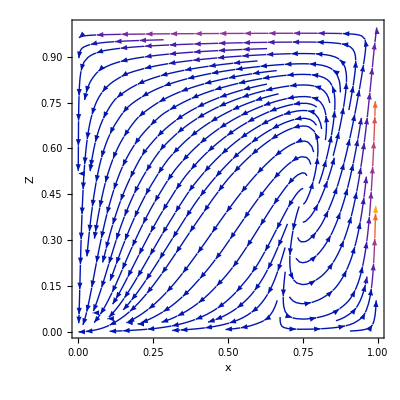

```mathematica
StreamPlot[{DE[wx,q,ϵ],DM[q]},{X,0,1},{Z,0,1},FrameLabel->{"x","Z"}]
```

### Compact x - y - z Phase Space

```mathematica
(*Define the parameters for this case*)
wx=-0.5;
q=1;
ϵ=-0.25;
```

```mathematica
(*Define the dynamical system for compact interacting dark matter (Z) and dark energy (X)*)
```

```mathematica
deX:=X'=-3*(Y/((1-Y^2)^(1/2)))*X*(1-X)*(1+wx+ϵ*(X/(1-X)))-q*X*(1-X)*(Z/(1-Z))*(Y/((1-Y^2)^(1/2)))
deY:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*((X/(1-X))+(Z/(1-Z))+3*wx*(X/(1-X))+3*ϵ*(X^2/((1-X)^2)))
deZ:=Z'=-3*Z*(1-Z)*(Y/((1-Y^2)^(1/2))) + q*(X/(1-X))*Z*(1-Z)*(Y/((1-Y^2)^(1/2)))
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{deX==0,deY==0,deZ==0},{X,Y,Z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Y→0.,Z→(1. X (2.+1. X))/(4.-6. X+5. X^2)},{X→0.666667,Y→-0.632456,Z→0.},{X→-2.,Y→0.,Z→0.},{X→0.,Y→0.,Z→0.},{X→0.666667,Y→0.632456,Z→0.},{X→0.75,Y→-0.745356,Z→0.428571},{X→0.75,Y→0.745356,Z→0.428571},{X→0.75,Y→0.,Z→0.891892}}

```mathematica
(*Remove arrows from fixed points and put them into a common variable name*)
FP[1]={X,Y/.FPs[[1,1]],Z/.FPs[[1,2]]};
FP[2]={X/.FPs[[2,1]],Y/.FPs[[2,2]],Z/.FPs[[2,3]]};
FP[3]={X/.FPs[[3,1]],Y/.FPs[[3,2]],Z/.FPs[[3,3]]};
FP[4]={X/.FPs[[4,1]],Y/.FPs[[4,2]],Z/.FPs[[4,3]]};
FP[5]={X/.FPs[[5,1]],Y/.FPs[[5,2]],Z/.FPs[[5,3]]};
FP[6]={X/.FPs[[6,1]],Y/.FPs[[6,2]],Z/.FPs[[6,3]]};
FP[7]={X/.FPs[[7,1]],Y/.FPs[[7,2]],Z/.FPs[[7,3]]};
FP[8]={X/.FPs[[8,1]],Y/.FPs[[8,2]],Z/.FPs[[8,3]]};
```

```mathematica
(*Put fixed points into a table*)
(*FPs=Table[FP[i],{i,11,18}];*)
```

```mathematica
(*Plot the fixed points of the system*)
FPShow=ListPointPlot3D[Table[FP[i],{i,2,8}], PlotStyle->{Black}];
```

```mathematica
(*Plot the fixed points from compactification*)
CompactFPShow=ListPointPlot3D[{{1,1,1},{1,-1,1},{0,1,1},{0,-1,1},{1,1,0},{1,-1,0},{0,1,0},{0,-1,0}}, PlotStyle->{Black}];
```

```mathematica
(*Plot the Einstein fixed points*)
EinsteinFPs=ParametricPlot3D[{X,0,(X *(2+ X))/(4-6* X+5* X^2)},{X,0,1},{Z,0,1},PlotStyle->{{Thickness[0.01],Red}}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[deX,X],D[deX,Y],D[deX,Z]}, {D[deY,X],D[deY,Y],D[deY,Z]},{D[deZ,X],D[deZ,Y],D[deZ,Z]}}];
J//MatrixForm
```

((Y (-1.5+X (6.-3. Z)+0.5 Z+X^2 (-4.5+2.5 Z)))/((-1.+X) √(1-Y^2) (-1.+Z)) | (X (-1.5+X (2.25-1.25 Z)+0.5 Z))/(√(1-Y^2) (-1.+Y^2) (-1.+Z)) | ((-1+X) X Y)/(√(1-Y^2) (-1+Z)^2)
(0.166667 (0.5+1. X) √(1-Y^2) (-1.+Y^2))/(-1.+X)^3 | (Y (2.-2.5 Z+Y^2 (-3.+3.5 Z)+X (-3.75+Y^2 (5.75-6.75 Z)+4.75 Z)+X^2 (2.125-2.625 Z+Y^2 (-3.125+3.625 Z))))/((-1.+X)^2 √(1-Y^2) (-1.+Z)) | -((1-Y^2)^(3/2))/(6 (-1+Z)^2)
-(Y (-1+Z) Z)/((-1+X)^2 √(1-Y^2)) | ((-3+4 X) (-1+Z) Z)/((-1+X) (1-Y^2)^(3/2)) | ((-3+4 X) Y (-1+2 Z))/((-1+X) √(1-Y^2)))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
(*FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{X->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]]}]//MatrixForm,Eigenvalues[J/.{X->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]]}]//MatrixForm,Eigenvectors[J/.{X->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]]}]//MatrixForm},{i,1,10}];*)
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
(*FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]*)
```

```mathematica
EqX[q_,wx_,ϵ_]=deX;
EqY[wx_,ϵ_]=deY;
EqZ[q_]=deZ;
```

```mathematica
PhaseSpace3D=StreamPlot3D[{EqX[q,wx,ϵ],EqY[wx,ϵ],EqZ[q]},{X,0,1},{Y,-1,1},{Z,0,1},AxesLabel->{"X","Y","Z"},StreamPoints->20(*RandomReal[{-1,1},{20,3}]*),StreamScale->{Full},StreamMarkers->"Arrow",StreamColorFunction->None];
```

Min::nord: Invalid comparison with -1.46372+1.38926×10^-7 ⅈ attempted.

Max::nord: Invalid comparison with -1.46372+1.38926×10^-7 ⅈ attempted.

```mathematica
Show[PhaseSpace3D,EinsteinFPs,FPShow,CompactFPShow]
```

-Graphics3D-

## Numeric Compact Phase Spaces

### Z = 0.009

```mathematica
(*Clear all variables*)
ClearAll["Global`*"];
```

```mathematica
(*Define the dynamical system for compact interacting dark matter (Z) and dark energy (X)*)
deXt:=X1'[t]==-3*(Y1[t]/((1-Y1[t]^2)^(1/2)))*X1[t]*(1-X1[t])*(1+wx+ϵ*(X1[t]/(1-X1[t])))-q*X1[t]*(1-X1[t])*Z1[t]/(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))
deYt:=Y1'[t]==-Y1[t]^2*(1-Y1[t]^2)^(1/2)-(((1-Y1[t]^2)^(3/2))/6)*((X1[t]/(1-X1[t]))+(Z1[t]/(1-Z1[t]))+3*wx*(X1[t]/(1-X1[t]))+3*ϵ*(X1[t]^2/((1-X1[t])^2)))
deZt:=Z1'[t]==-3*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2))) + q*(X1[t]/(1-X1[t]))*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))
deAt:=A1'[t]==A1[t]*(1-A1[t])*Y1[t]/((1-Y1[t])^(1/2))
```

```mathematica
q=1;
wx=-0.5;
ϵ=-0.25;
```

```mathematica
(*Plot the fixed points*)
(*FPShow=ListPlot[{{3/(3+q),-(√(-q *wx-3* ϵ))/(√(q^2-q *wx-3* ϵ))},{3/(3+q),(√(-q *wx-3 ϵ))/(√(q^2-q* wx-3 ϵ))},{0,0},{(1+wx)/(1+wx-ϵ),0},{(1+3 wx)/(1+3 wx-3 ϵ),0},{(1+wx)/(1+wx-ϵ),-(√(1+wx))/(√(1+wx-3 ϵ))},{(1+wx)/(1+wx-ϵ),(√(1+wx))/(√(1+wx-3 ϵ))},{3/(3+q),0},{(6+q+6 wx+3 q wx-3 ϵ+√(q^2+6 q^2 wx+9 q^2 wx^2+30 q ϵ+18 q wx ϵ+9 ϵ^2))/(2 (3+q+3 wx+3 q wx-3 ϵ-3 q ϵ)),0},{(6+q+6 wx+3 q wx-3 ϵ-√(q^2+6 q^2 wx+9 q^2 wx^2+30 q ϵ+18 q wx ϵ+9 ϵ^2))/(2 (3+q+3 wx+3 q wx-3 ϵ-3 q ϵ)),0}},PlotMarkers->{Automatic,Small},PlotStyle->{Black}]*)
```

```mathematica
traj[X0_,Y0_,Z0_,A0_]=NDSolve[{deXt,deYt,deZt,deAt, X1[0]==X0,Y1[0]==Y0,Z1[0]==Z0,A1[0]==A0}, {X1,Y1,Z1,A1},{t,-80,80},AccuracyGoal->5,PrecisionGoal->5,MaxSteps->10000];
```

NDSolve::ndinnt: Initial condition A0 is not a number or a rectangular array of numbers.

```mathematica
sol[1]=traj[0.1,0.1,0.009,1/Sqrt[2]];
sol[2]=traj[0.8,0.75,0.009,1/Sqrt[2]];
sol[3]=traj[0.6,0.65,0.009,1/Sqrt[2]];
sol[4]=traj[0.5,0.1,0.009,1/Sqrt[2]];
sol[5]=traj[0.5,0.3,0.009,1/Sqrt[2]];
sol[6]=traj[0.5,0.741,0.009,1/Sqrt[2]]; 
sol[7]=traj[0.5,0.8,0.009,1/Sqrt[2]];
sol[8]=traj[0.1,0.5,0.009,1/Sqrt[2]];
sol[9]=traj[0.02,0.5,0.009,1/Sqrt[2]];
sol[10]=traj[0.02,0.8,0.009,1/Sqrt[2]];
```

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == -1.78598.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == -1.06567.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == -0.796861.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == -1.97181.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == -1.73773.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == -0.835388.

```mathematica
sol[11]=traj[0.1,-0.1,0.009,1/Sqrt[2]];
sol[12]=traj[0.8,-0.75,0.009,1/Sqrt[2]];
sol[13]=traj[0.6,-0.65,0.009,1/Sqrt[2]];
sol[14]=traj[0.5,-0.1,0.009,1/Sqrt[2]];
sol[15]=traj[0.5,-0.3,0.009,1/Sqrt[2]];
sol[16]=traj[0.5,-0.741,0.009,1/Sqrt[2]]; 
sol[17]=traj[0.5,-0.8,0.009,1/Sqrt[2]];
sol[18]=traj[0.1,-0.5,0.009,1/Sqrt[2]];
sol[19]=traj[0.02,-0.5,0.009,1/Sqrt[2]];
sol[20]=traj[0.02,-0.8,0.009,1/Sqrt[2]];
```

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 1.63862.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 1.00058.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 0.822162.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 1.78606.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 1.82204.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 0.75006.

```mathematica
sol[21]=traj[0.5,0.741,0.009,1/Sqrt[2]]; 
sol[22]=traj[0.5,-0.741,0.009,1/Sqrt[2]];
```

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == -1.06567.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 1.00058.

```mathematica
PhaseSpacexy=ParametricPlot[Evaluate[Table[{X1[t],Y1[t]}/.sol[i],{i,1,20}], {t,-80,80},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotRange->{{-0.1,1.1},{-1.1,1.1}},AxesLabel->{"X","Y"}];
```

InterpolatingFunction::dmval: Input value {-79.9967} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
PhaseSpaceFFS=ParametricPlot[Evaluate[Table[{X1[t],Y1[t]}/.sol[i],{i,21,22}], {t,-80,80},PlotStyle -> {{Darker[Green]}}],PlotRange->{{-0.1,1.1},{-1.1,1.1}},AxesLabel->{"X","Y"}];
```

InterpolatingFunction::dmval: Input value {-79.9967} lies outside the range of data in the interpolating function. Extrapolation will be used.

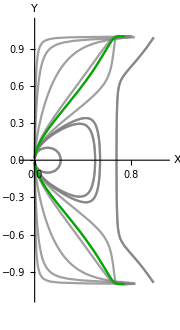

```mathematica
Show[PhaseSpacexy,PhaseSpaceFFS]
```

InterpolatingFunction::dmval: Input value {-79.9967} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

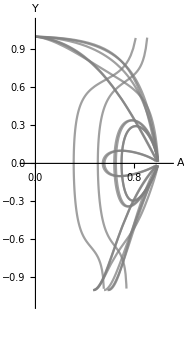

```mathematica
(*Plot A-Y phase space*)
PhaseSpaceay=ParametricPlot[Evaluate[Table[{A1[t],Y1[t]}/.sol[i],{i,1,20}], {t,-80,80},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotRange->{{-0.1,1.1},{-1.1,1.1}},AxesLabel->{"A","Y"}]
```

### Z = 0.9

```mathematica
(*Clear all variables*)
ClearAll["Global`*"];
```

```mathematica
(*Define the dynamical system for compact interacting dark matter (Z) and dark energy (X)*)
deXt:=X1'[t]==-3*(Y1[t]/((1-Y1[t]^2)^(1/2)))*X1[t]*(1-X1[t])*(1+wx+ϵ*(X1[t]/(1-X1[t])))-q*X1[t]*(1-X1[t])*Z1[t]/(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))
deYt:=Y1'[t]==-Y1[t]^2*(1-Y1[t]^2)^(1/2)-(((1-Y1[t]^2)^(3/2))/6)*((X1[t]/(1-X1[t]))+(Z1[t]/(1-Z1[t]))+3*wx*(X1[t]/(1-X1[t]))+3*ϵ*(X1[t]^2/((1-X1[t])^2)))
deZt:=Z1'[t]==-3*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2))) + q*(X1[t]/(1-X1[t]))*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))
deAt:=A1'[t]==A1[t]*(1-A1[t])*Y1[t]/((1-Y1[t])^(1/2))
```

```mathematica
q=1;
wx=-0.5;
ϵ=-0.25;
```

```mathematica
traj[X0_,Y0_,Z0_,A0_]=NDSolve[{deXt,deYt,deZt,deAt, X1[0]==X0,Y1[0]==Y0,Z1[0]==Z0,A1[0]==A0}, {X1,Y1,Z1,A1},{t,-80,80},AccuracyGoal->5,PrecisionGoal->5,MaxSteps->10000];
```

NDSolve::ndinnt: Initial condition A0 is not a number or a rectangular array of numbers.

```mathematica
sol[1]=traj[0.1,0.1,0.9,1/Sqrt[2]];
sol[2]=traj[0.8,0.75,0.9,1/Sqrt[2]];
sol[3]=traj[0.6,0.65,0.9,1/Sqrt[2]];
sol[4]=traj[0.5,0.1,0.9,1/Sqrt[2]];
sol[5]=traj[0.5,0.3,0.9,1/Sqrt[2]];
sol[6]=traj[0.5,0.741,0.9,1/Sqrt[2]]; 
sol[7]=traj[0.5,0.8,0.9,1/Sqrt[2]];
sol[8]=traj[0.1,0.5,0.9,1/Sqrt[2]];
sol[9]=traj[0.02,0.5,0.9,1/Sqrt[2]];
sol[10]=traj[0.02,0.8,0.9,1/Sqrt[2]];
```

```mathematica
sol[11]=traj[0.02,0.554,0.9,1/Sqrt[2]]; 
sol[12]=traj[0.02,-0.554,0.9,1/Sqrt[2]];
```

```mathematica
PhaseSpacexy2=ParametricPlot[Evaluate[Table[{X1[t],Y1[t]}/.sol[i],{i,1,10}], {t,-80,80},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotRange->{{-0.1,1.1},{-1.1,1.1}},AxesLabel->{"X","Y"}];
```

```mathematica
PhaseSpaceFFS2=ParametricPlot[Evaluate[Table[{X1[t],Y1[t]}/.sol[i],{i,11,12}], {t,-80,80},PlotStyle -> {{Darker[Green]}}],PlotRange->{{-0.1,1.1},{-1.1,1.1}},AxesLabel->{"X","Y"}];
```

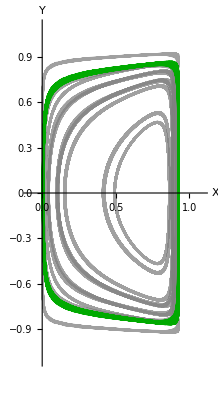

```mathematica
Show[PhaseSpacexy2,PhaseSpaceFFS2]
```

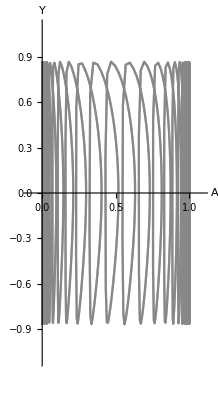

```mathematica
PhaseSpacexy2=ParametricPlot[Evaluate[Table[{A1[t],Y1[t]}/.sol[12],{i,1,2}], {t,-80,80},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotRange->{{-0.1,1.1},{-1.1,1.1}},AxesLabel->{"A","Y"}]
```